```mathematica
ClearAll["Global`*"]
```

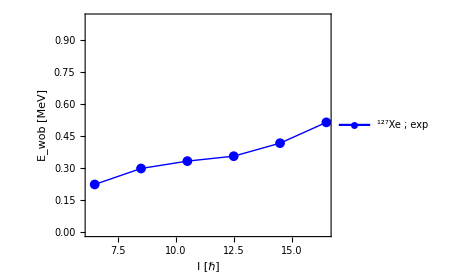

```mathematica
yrastEn=Sort[{5098.9,4137.7,3202.7,2312.9,1508.8,828.1,309}];
wob1En=Sort[{5132.0,4086.7,3113.5,2243.5,1466.7,792.2}];;
yrastSpin=Table[i/2,{i,11,35,4}];
wob1Spin=Table[i/2,{i,13,33,4}];
wobbling[yrast_,b1_,spins_]:=Table[{spins[[i]],b1[[i]]/1000-1/2(yrast[[i]]+yrast[[i+1]])/1000},{i,1,Length[b1]}];
data=wobbling[yrastEn,wob1En,wob1Spin];
fig=ListPlot[data,Joined->True,PlotMarkers->{Automatic, Medium},Frame->True,Axes->False,AspectRatio->0.8,PlotStyle->{Thick,Blue},FrameStyle->Directive[Thick,Black],FrameLabel->{"I [ℏ]","E_wob [MeV]"},LabelStyle->{20,Bold,Black},PlotLegends->Placed[{Style[Row[{Superscript["","127"],"Xe ; exp"}],30]},{0.4,0.85}],ImageSize->350,PlotRange->{Full,{0,1}}];
Export["/Users/basavyr/Documents/Work/DFT/mathematica-useful-algorithms/Physics/experimental-data-collection-wobblers/127Xe.pdf",fig];
Show[fig]
```